```mathematica
{RandomReal[{0,1},100]}//Image[#,ImageSize->Full]&//Binarize[#,.85]&
```

-Graphics-

Simulation of a 1 - d  percolation

<|17→1,18→1,16→9,15→10,14→33,13→49,12→93,11→162,10→324,9→672,8→1255,7→2377,6→4567,5→8717,4→16712,3→32595,2→62063,1→119496|>

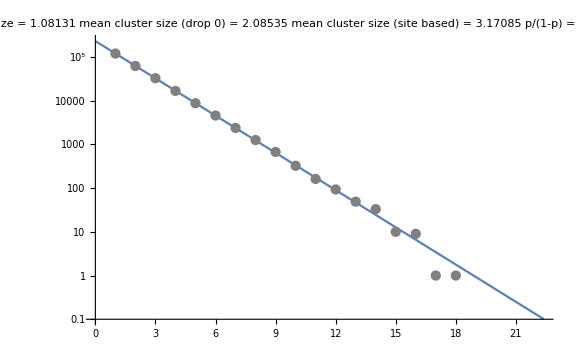

```mathematica
Clear[n,p,s,c,minus,l]
Module[{n=10^6,p=0.52,s,c,minus,l},
s=Join[RandomReal[{0,1},n]]/.{a_/;a>=p->"- ",a_/;a<p->"+"}//StringJoin//StringSplit;
c=(StringLength[StringReplace[{"-"->""," "->""}]/@s]//Counts//Sort);
l=Delete[c,Key[0]];
Print[l];
w=Values[c];
w1=Values@l;
num=Keys[c];
num1=Keys@l;
Show[LogPlot[n*(1-p)^2 p^s,{s,0,-Log[10n (-1+p)^2]/Log[p]},PlotLabel->"length = "<>ToString[n]<>"  p = "<>ToString[p]<>"
mean cluster size = "<>ToString[Mean[WeightedData[num,w]//N]]<>"
mean cluster size (drop 0) = "<>ToString[Mean[WeightedData[num1,w1]//N]]<>"
mean cluster size (site based) = "<>ToString[Mean[WeightedData[num,num*w]//N]]<>"
p/(1-p) = "<>ToString[p/(1.-p)]<>"  and  1/(1-p) = "<>ToString[1/(1-p)]<>"
(1+p)/(1-p) = "<>ToString[(1+p)/(1.-p)],ImageSize->Large],ListLogPlot[l,PlotStyle->Gray]]]
```